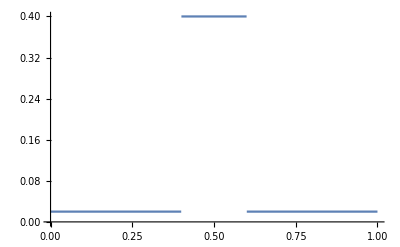

```mathematica
epsilon =0.1; alphaRod =0.4; alphaSheet = 0.02;
diffusionConst[x_]:=Piecewise[{{alphaSheet, x < 0.5-epsilon},{alphaRod,x ≥ 0.5-epsilon && x < 0.5 + epsilon},{alphaSheet,x≥0.5+epsilon}}];
Plot[diffusionConst[x],{x,0,1}]
```

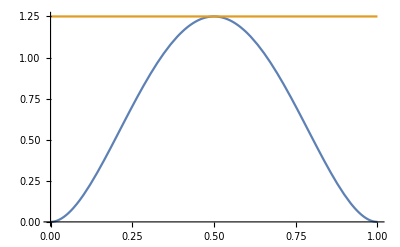

```mathematica
kk = 20;
initTemp[x_]:=kk*x^2*(x-1)^2;
maxTempVal = initTemp[0.5];
Plot[{initTemp[x],maxTempVal},{x,0,1}]
```

```mathematica
valuesNoRod = NDSolveValue[{D[u[x,t],t]-alphaSheet*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==initTemp[x],t==0]},u,{x,0,1},{t,0,10}]; 
valuesWithRod = NDSolveValue[{D[u[x,t],t]-diffusionConst[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==initTemp[x],t==0]},u,{x,0,1},{t,0,10}];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
Manipulate[Plot[{valuesNoRod[x,t],valuesWithRod[x,t],maxTempVal,0},{x,0,1},PlotLegends->{"Temp with No Rod","Temp with Rod","Max","Min"}],{t,0,10}]
```

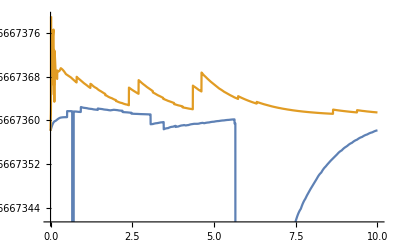

```mathematica
totalEnergyWithRod[t_]:=Integrate[valuesWithRod[x,t],{x,0,1}];totalEnergyNoRod[t_]:=Integrate[valuesNoRod[x,t],{x,0,1}];
Plot[{totalEnergyNoRod[t],totalEnergyWithRod[t]},{t,0,10}]
```

```mathematica
energyFlowXNoRod[x_,t_]:=D[valuesNoRod[xx,tt],xx]/.{xx->x,tt->t};
energyFlowXWithRod[x_,t_]:=D[valuesWithRod[xx,tt],xx]/.{xx->x,tt->t};Manipulate[Plot[{energyFlowXNoRod[x,t],energyFlowXWithRod[x,t],maxTempVal,0},{x,0,1},PlotLegends->{"Temp Flow with No Rod","Temp Flow with Rod","Max","Min"}],{t,0,10}]
```

```mathematica
energyFluxXNoRod[x_,t_]:=Laplacian[valuesNoRod[xx,tt],{xx}]/.{xx->x,tt->t};
energyFluxXWithRod[x_,t_]:=Laplacian[valuesWithRod[xx,tt],{xx}]/.{xx->x,tt->t};Manipulate[Plot[{energyFluxXNoRod[x,t],energyFluxXWithRod[x,t],maxTempVal,0},{x,0,1},PlotLegends->{"Temp Flow with No Rod","Temp Flow with Rod","Max","Min"}],{t,0,10}]
```

```mathematica
energyFluxXNoRod2[x_,t_]:=D[valuesNoRod[xx,tt],tt]/.{xx->x,tt->t};
energyFluxXWithRod2[x_,t_]:=D[valuesWithRod[xx,tt],tt]/.{xx->x,tt->t};Manipulate[Plot[{energyFluxXNoRod2[x,t],energyFluxXWithRod2[x,t],maxTempVal,0},{x,0,1},PlotLegends->{"Temp Flow with No Rod","Temp Flow with Rod","Max","Min"}],{t,0,10}]
```